```mathematica
ClearAll[f0,m1,m2,mchirp,M,r,d];
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
M=mchirp[m1,m2]*4.92549095*10^-6;
d=r*1.0292712503*10^8;
tmerg[M_,f0_]=5(256(N[π]f0)^(8/3)M^(5/3))^-1;
F[M_,f0_,t_]=(M (f0)^9)^(1/8)((M f0)^(1/3)-256f0^3 M^2N[π]^(8/3)(t/5))^(-3/8);
Angle[M_,f0_,t_]=-2((256(N[π]M f0)^(8/3))^(-1)-(t/(5M)))^(5/8);
Amplitude[M_,f0_,d_,t_]=4M^(5/3)N[π]^(2/3)(F[M,f0,t])^(2/3)d^(-1 );
```

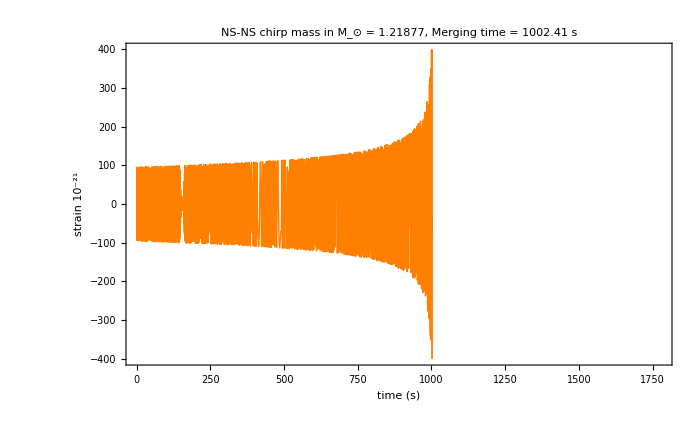

```mathematica
m1 = 1.4;
m2 = 1.4;
r = 8* 10^3;
f0 = 10;
Needs["PlotLegends`"]
p1=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*(10^21)} ,{t,0,tmerg[M,f0]},PlotLabel->Row[{" NS-NS chirp mass in ",Subscript[Style["M", Italic],"⊙"]," = ",  N[mchirp[m1,m2]],", Merging time = ",  tmerg[M,f0]"s"}],
PlotStyle->{Orange},Frame->True,ImageSize->700 ,PlotRange->{{0,1780},{-400,400}},BaseStyle ->{FontFamily->"Arial",16},
FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] )" strain " ,18]}]
```

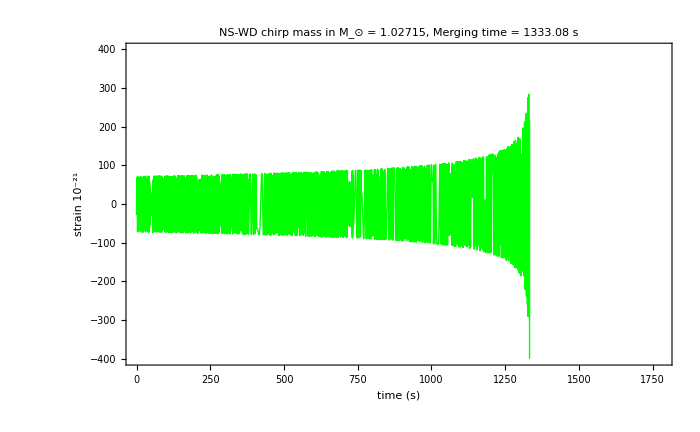

```mathematica
m1 = 1;
m2 = 1.4;
r = 8*10^3;
f0 = 10;

p2=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*10^21} ,{t,0,tmerg[M,f0]},
PlotLabel->Row[{" NS-WD chirp mass in ",Subscript[Style["M", Italic],"⊙"]," = ",  N[mchirp[m1,m2]],", Merging time = ",  tmerg[M,f0]"s"}],
PlotStyle->{Green},Frame->True,ImageSize->700 ,PlotRange->{{0,1780},{-400,400}},BaseStyle ->{FontFamily->"Arial",16},
 FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] )" strain " ,18]}]
```

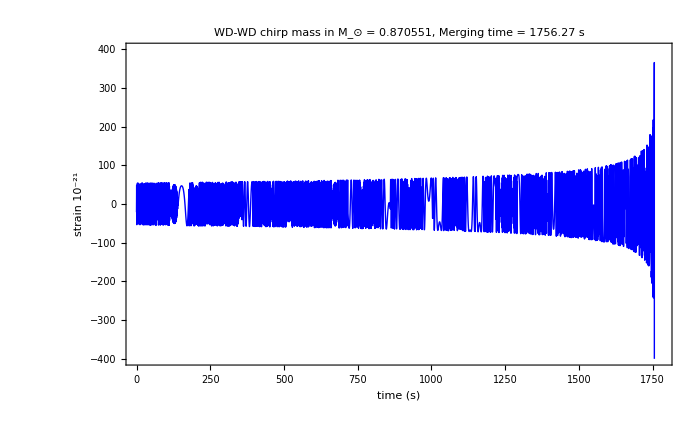

```mathematica
m1 = 1;
m2 = 1;
r = 8* 10^3;
f0 = 10;

p3=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*10^21} ,{t,0,tmerg[M,f0]},
PlotLabel->Row[{" WD-WD chirp mass in ",Subscript[Style["M", Italic],"⊙"]," = ",  N[mchirp[m1,m2]],", Merging time = ",  tmerg[M,f0]"s"}],
PlotStyle->{Blue},Frame->True,ImageSize->700 ,PlotRange->{{0,1780},{-400,400}},BaseStyle ->{FontFamily->"Arial",16},FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] ) "strain " ,18]}]
```

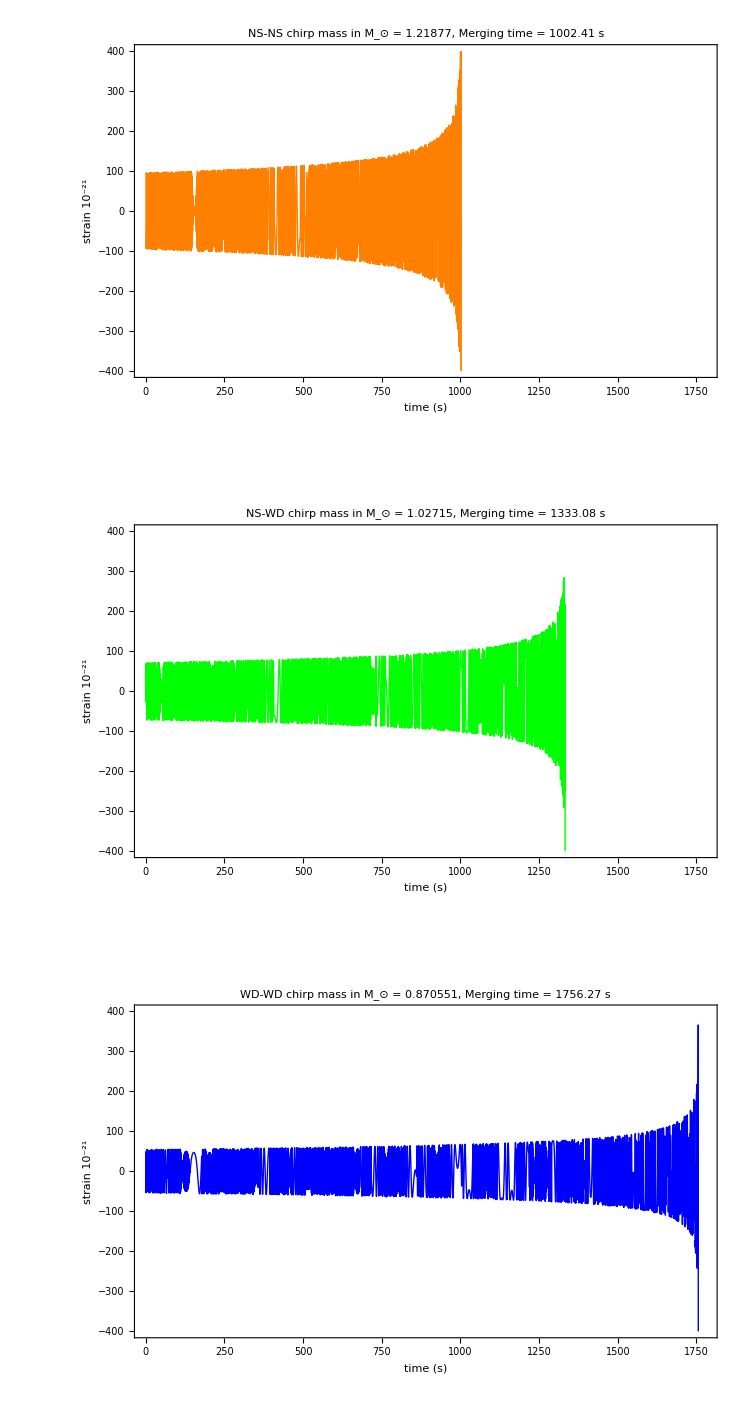

```mathematica
h9=GraphicsColumn[{p1,p2,p3}]
```

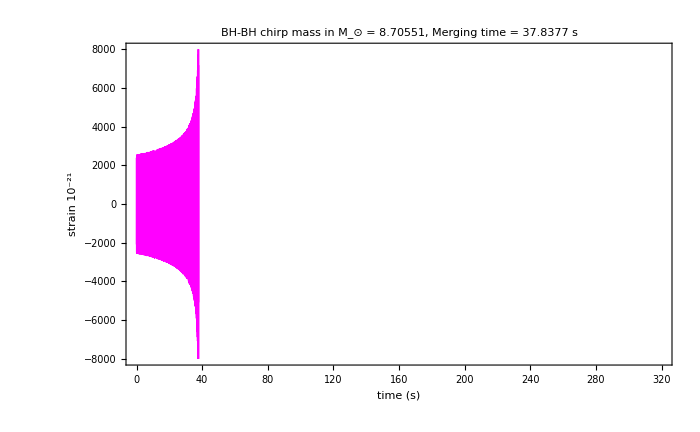

```mathematica
m1 = 10;
m2 = 10;
r = 8* 10^3;
f0 = 10;

p4=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*10^21} ,{t,0,tmerg[M,f0]},
PlotLabel->Row[{" BH-BH chirp mass in ",Subscript[Style["M", Italic],"⊙"]," = ",  N[mchirp[m1,m2]],", Merging time = ",  tmerg[M,f0]"s"}],
PlotStyle->{Magenta},Frame->True,ImageSize->700 ,PlotRange->{{0,320},{-8000,8000}},BaseStyle ->{FontFamily->"Arial",16},FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] ) "strain " ,18]}]
```

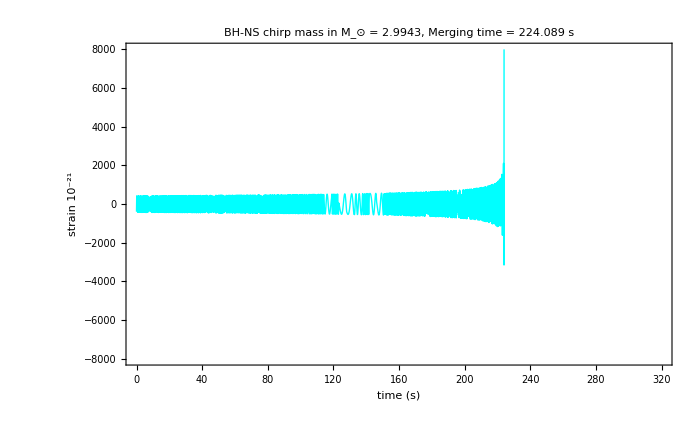

```mathematica
m1 = 10;
m2 = 1.4;
r = 8* 10^3;
f0 = 10;

p5=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*10^21} ,{t,0,tmerg[M,f0]},
PlotLabel->Row[{" BH-NS chirp mass in ",Subscript[Style["M", Italic],"⊙"]," = ",  N[mchirp[m1,m2]],", Merging time = ",  tmerg[M,f0]"s"}],
PlotStyle->{Cyan},Frame->True,ImageSize->700 ,PlotRange->{{0,320},{-8000,8000}},BaseStyle ->{FontFamily->"Arial",16},
FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] ) "strain " ,18]}]
```

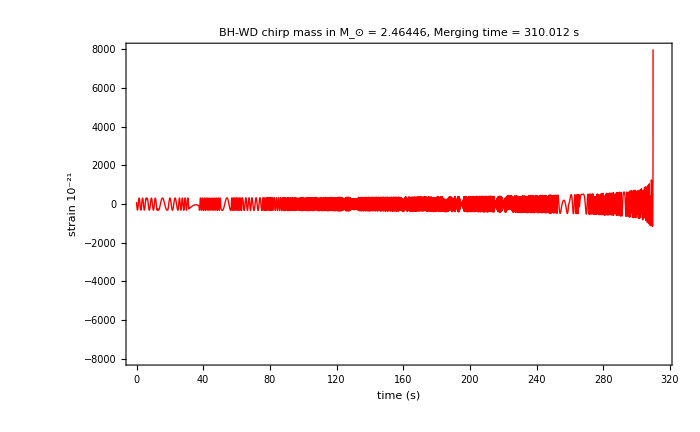

```mathematica
m1 = 10;
m2 = 1;
r = 8* 10^3;
f0 = 10;

p6=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*10^21} ,{t,0,tmerg[M,f0]},
PlotLabel->Row[{" BH-WD chirp mass in ",Subscript[Style["M", Italic],"⊙"]," = ",  N[mchirp[m1,m2]],", Merging time = ",  tmerg[M,f0]"s"}],PlotStyle->{Red},Frame->True,ImageSize->700 ,PlotRange->{{0,315},{-8000,8000}},BaseStyle ->{FontFamily->"Arial",16},
FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] ) "strain " ,18]}]
```

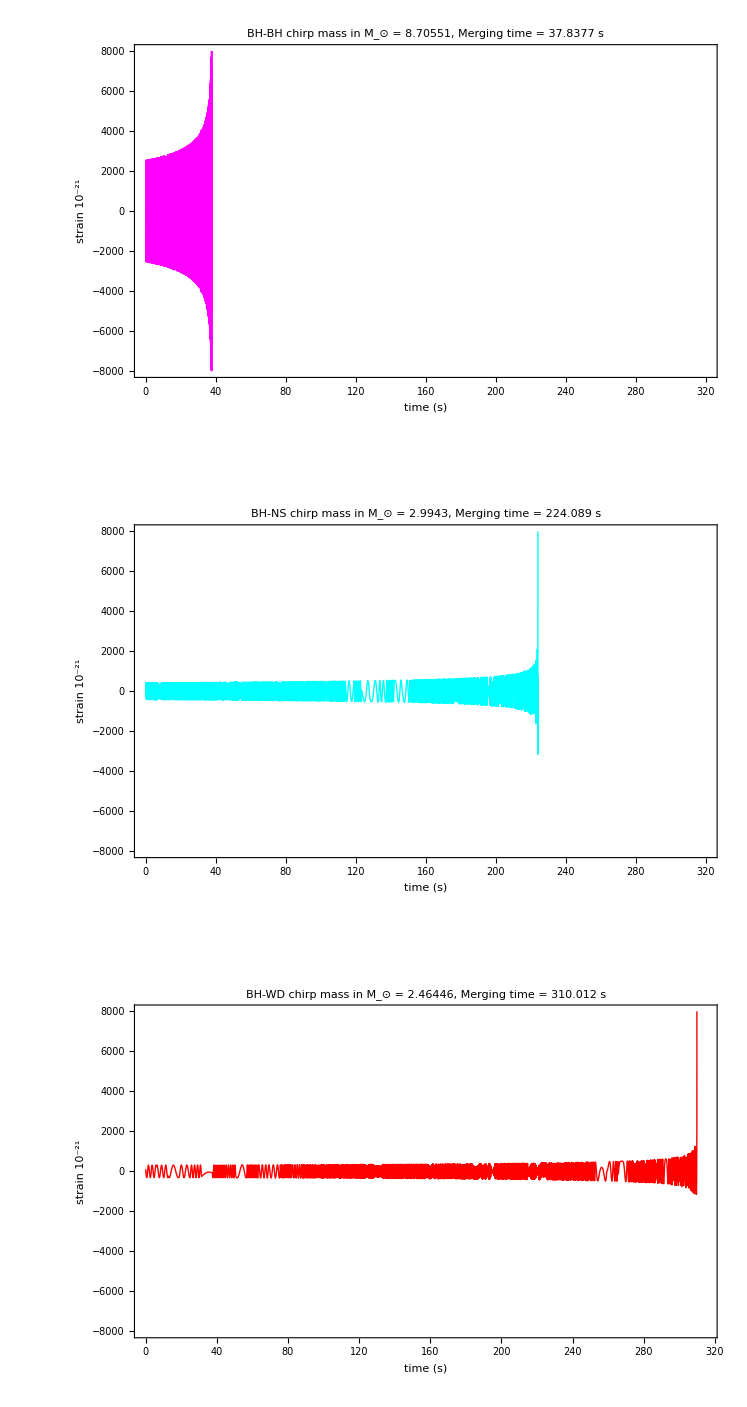

```mathematica
GraphicsColumn[{p4,p5,p6}]
```

```mathematica
ClearAll[f0,m1,m2,mchirp,M,r,d];
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
M=mchirp[m1,m2]*4.92549095*10^-6;
d=r*1.0292712503*10^8;
tmerg[M_,f0_]=5(256(N[π]f0)^(8/3)M^(5/3))^-1;
F[M_,f0_,t_]=(M (f0)^9)^(1/8)((M f0)^(1/3)-256f0^3 M^2N[π]^(8/3)(t/5))^(-3/8);
Angle[M_,f0_,t_]=-2((256(N[π]M f0)^(8/3))^(-1)-(t/(5M)))^(5/8);
Amplitude[M_,f0_,d_,t_]=4M^(5/3)N[π]^(2/3)(F[M,f0,t])^(2/3)d^(-1 );
```

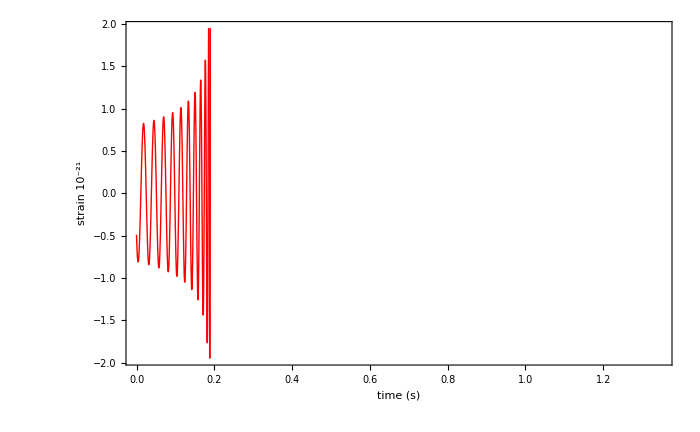

```mathematica
m1 = 36;
m2 = 29;
r = 410* 10^6;
f0 = 35;
Needs["PlotLegends`"]
p10=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*(10^21)} ,{t,0,tmerg[M,f0]},PlotRange->{{0,1.35},{-1.95,1.95}},
PlotStyle->{Red,Thickness[Large]},Frame->True,ImageSize->700 ,BaseStyle ->{FontFamily->"Arial",16},
FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] )" strain " ,18]}]
```

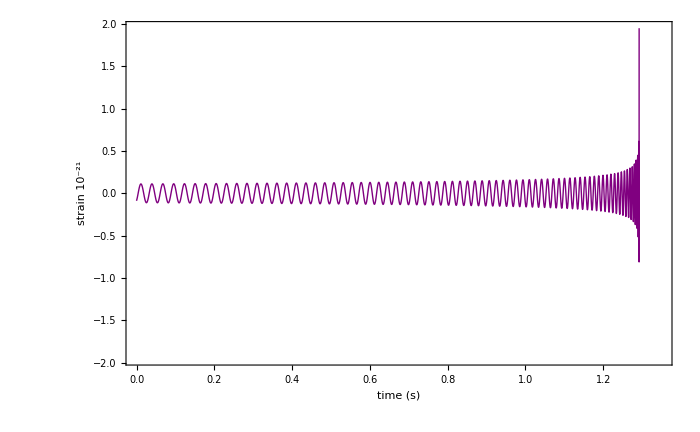

```mathematica
m1 = 14.2;
m2 = 7.5;
r = 440* 10^6;
f0 = 35;
Needs["PlotLegends`"]
p11=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*(10^21)} ,{t,0,tmerg[M,f0]},PlotRange->{{0,1.35},{-1.95,1.95}},
PlotStyle->{Purple,Thickness[Large]},Frame->True,ImageSize->700 ,BaseStyle ->{FontFamily->"Arial",16},
FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] )" strain " ,18]}]
```

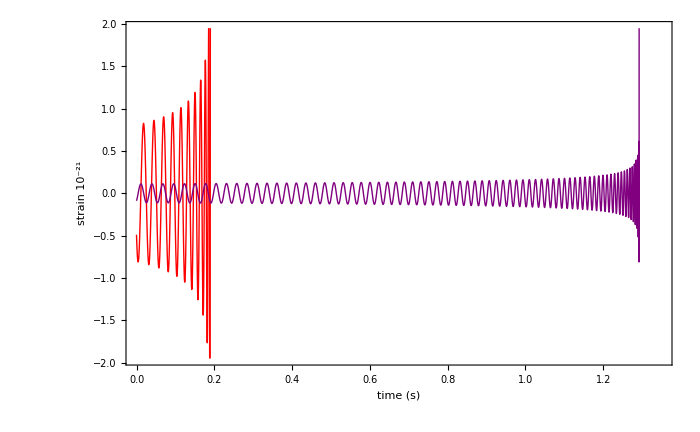

```mathematica
p13=Show[p10,p11]
```

```mathematica
ClearAll[m1,m2]
Needs["PlotLegends`"]
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
f0=35;
myplotfn2[m1_,m2_,t_]= ((mchirp[m1,m2]*4.92549095*10^-6)*f0^9)^(1/8)(((mchirp[m1,m2]*4.92549095*10^-6)* f0)^(1/3)-256f0^3 (mchirp[m1,m2]*4.92549095*10^-6)^2N[π]^(8/3)(t/5))^(-3/8);
```

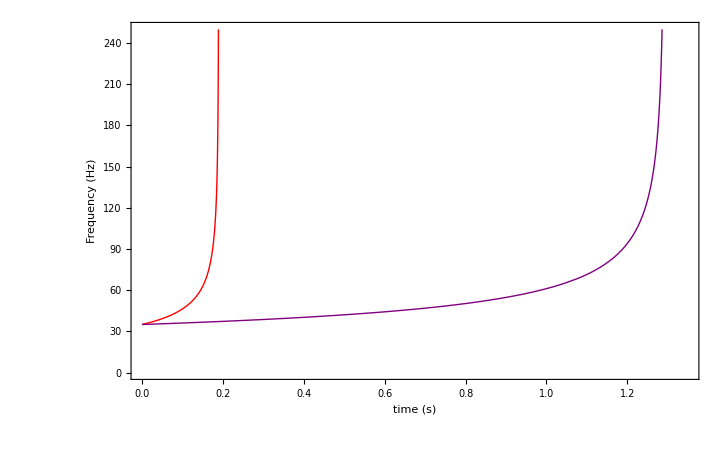

```mathematica
Needs["PlotLegends`"]
p12=Plot[{myplotfn2[36,29,t],myplotfn2[14.2,7.5,t]}
,{t,0,1.35},PlotStyle->{{Thickness[Large],Red},{Thickness[Large],Purple}},PlotRange->{{0,1.35},{0,250}},Frame->True,ImageSize->728.5,BaseStyle ->{FontFamily->"Arial",16},FrameLabel->{Style["time (s)",18],Style["Frequency (Hz)",18]}]
```

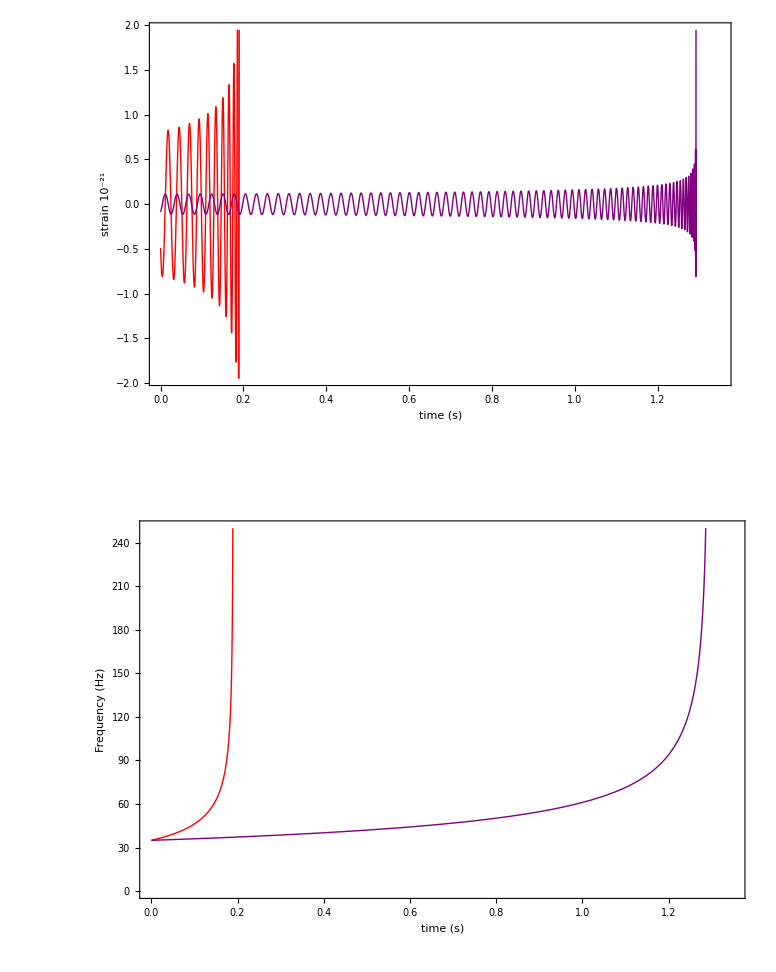

-Graphics-

```mathematica
GraphicsColumn[{p13,p12}]
```

```mathematica
|
```

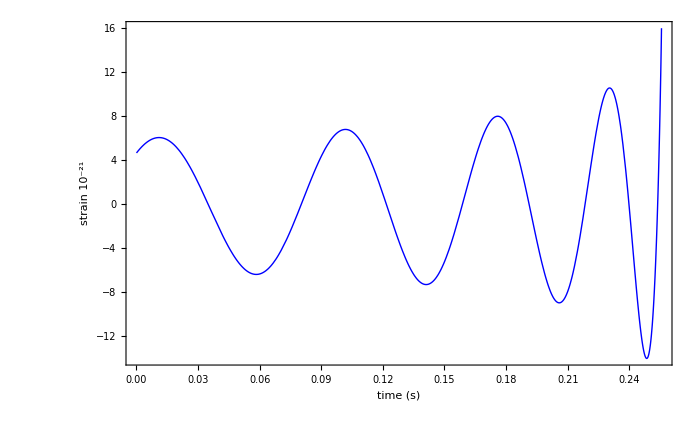

```mathematica
m1 =200;
m2 = 200;
r =500* 10^6;
f0 = 10;
Needs["PlotLegends`"]
p15=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*(10^21)} ,{t,0,tmerg[M,f0]},PlotRange->{{0,0.84},{16,-16}},
PlotStyle->{Blue,Thickness[Large]},Frame->True,ImageSize->700 ,BaseStyle ->{FontFamily->"Arial",16},
FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] )" strain " ,18]}]
```

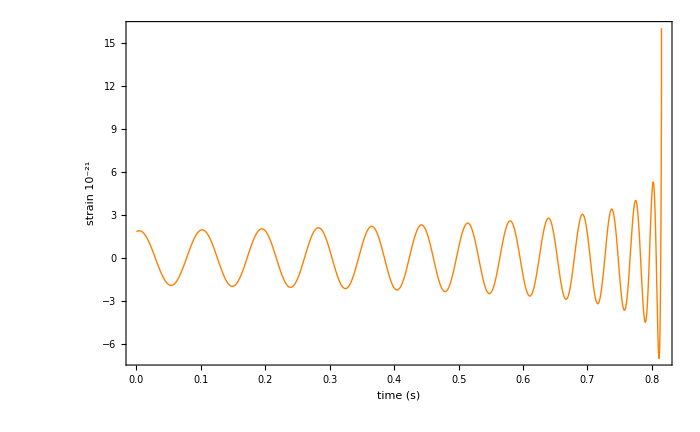

```mathematica
m1 =100;
m2 = 100;
r =500* 10^6;
f0 = 10;
Needs["PlotLegends`"]
p16=Plot[{Amplitude[M,f0,d,t]*Cos[Angle[M,f0,t]]*(10^21)} ,{t,0,tmerg[M,f0]},PlotRange->{{0,0.84},{16,-16}},
PlotStyle->{Orange,Thickness[Large]},Frame->True,ImageSize->700 ,BaseStyle ->{FontFamily->"Arial",16},
FrameLabel->{Style["time (s)",18],Style[(Subsuperscript["10","","-21"] )" strain " ,18]}]
```

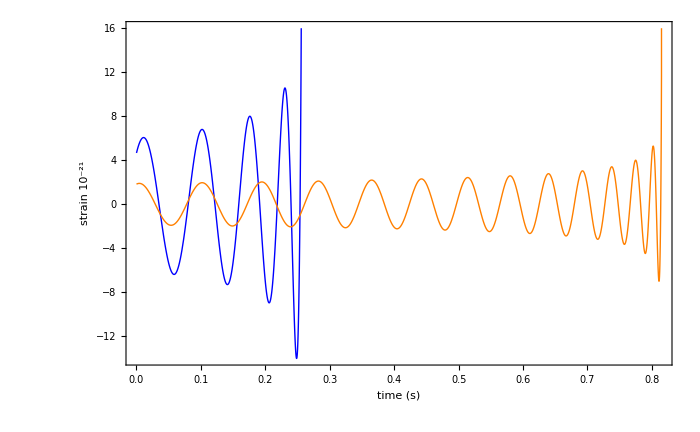

```mathematica
p17=Show[p15,p16]
```

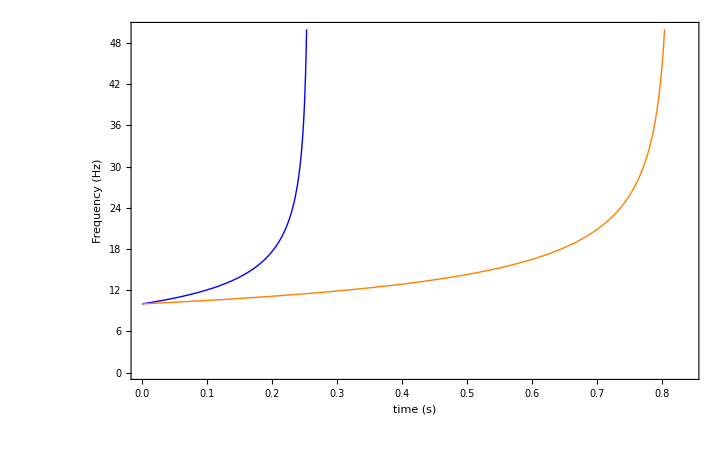

```mathematica
ClearAll[m1,m2]
Needs["PlotLegends`"]
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
f0=10;
myplotfn2[m1_,m2_,t_]= ((mchirp[m1,m2]*4.92549095*10^-6)*f0^9)^(1/8)(((mchirp[m1,m2]*4.92549095*10^-6)* f0)^(1/3)-256f0^3 (mchirp[m1,m2]*4.92549095*10^-6)^2N[π]^(8/3)(t/5))^(-3/8);
p18=Plot[{myplotfn2[200,200,t],myplotfn2[100,100,t]}
,{t,0,0.9},PlotStyle->{{Thickness[Large],Blue},{Thickness[Large],Orange}},PlotRange->{{0,0.84},{0,50}},Frame->True,ImageSize->728.5,BaseStyle ->{FontFamily->"Arial",16},FrameLabel->{Style["time (s)",18],Style["Frequency (Hz)",18]}]
```

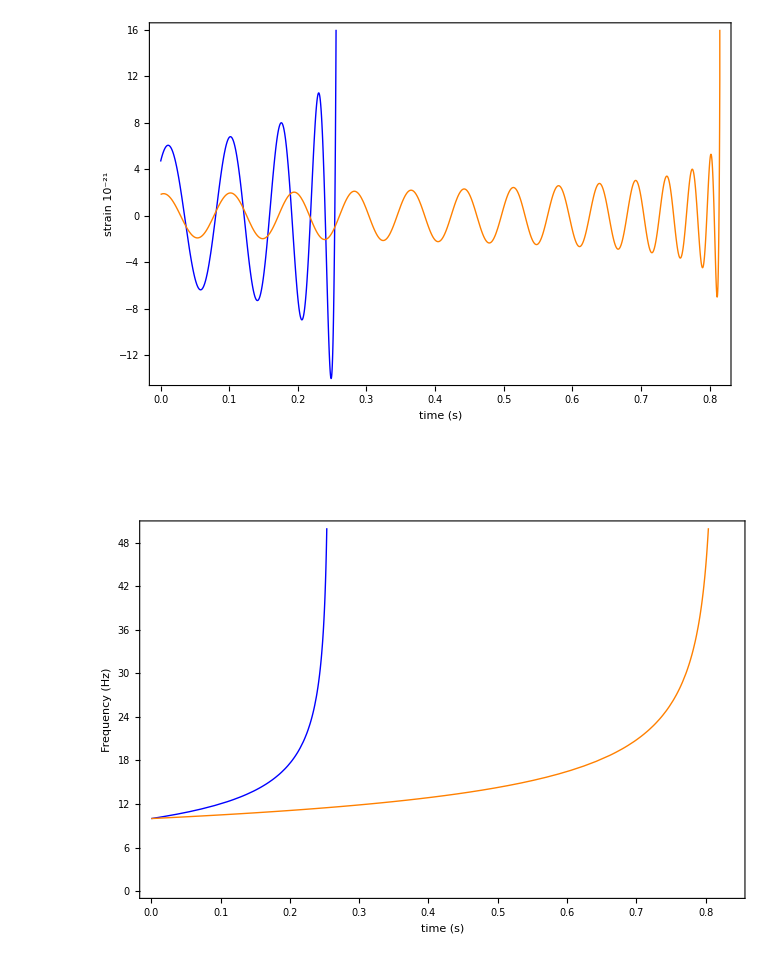

-Graphics-

```mathematica
GraphicsColumn[{p17,p18}]
```